# check the sign of rho_c

## First we try some simple plots, considering a single constant bin for q_v

```mathematica
(*define the density parameters*)
ΩΛ[a_] := 1-Ωc-Ωb;
Ωb=0.05;
```

```mathematica
(* Subscript[ρ, c] for a single constant bin*)
rhoc[a_,qv_]:=Ωc a^(-3) +ΩΛ[a] qv/(qv-3) (a^(-3) - a^(-qv));
```

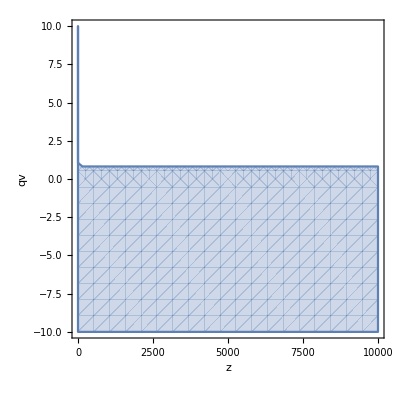

```mathematica
(* plot for sign[Subscript[ρ, c]] > 0 fixing Subscript[Ω, c] and varying z and Subscript[q, v]*)
RegionPlot[Evaluate[rhoc[1/(z+1),qv ]/.{Ωc->0.26}]≥  0,{z,0,10^4},{qv,-10,10}, Frame->True, FrameLabel->{"z","qv"}, PlotLegends->"ρ_c>0"]
```

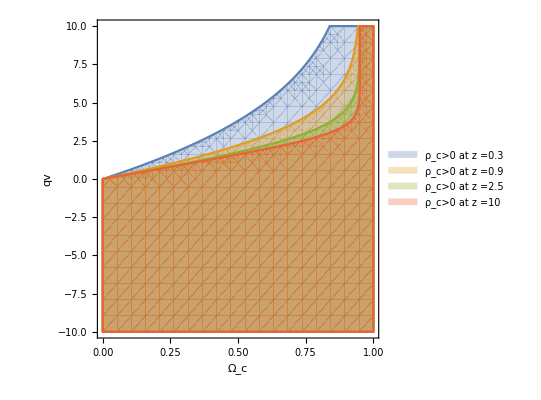

```mathematica
(* We now fix different values of z and vary Subscript[Ω, c] and Subscript[q, v]*)
RegionPlot[{Evaluate[rhoc[1/(z+1),qv ]/.{z->0.3}]≥  0,Evaluate[rhoc[1/(z+1),qv ]/.{z->0.9}]≥  0,Evaluate[rhoc[1/(z+1),qv ]/.{z->2.5}]≥  0,Evaluate[rhoc[1/(z+1),qv ]/.{z->10}]≥  0},{Ωc,0,1},{qv,-10,10}, Frame->True, FrameLabel->{"Ω_c","qv"}, PlotLegends->{"ρ_c>0 at z =0.3","ρ_c>0 at z =0.9","ρ_c>0 at z =2.5","ρ_c>0 at z =10"}]
```

```mathematica
(* 3D Plot where we vary all three parameters at the same time*)
ClearAll[ρc,Ωc]
ρc[a_,qv_,Ωc_]:=Ωc a^(-3) +ΩΛ[a] qv/(qv-3) (a^(-3) - a^(-qv));
RegionPlot3D[Evaluate[ρc[1/(z+1),qv,Ωc ]]≥  0,{z,0,.3},{qv,0,2}, {Ωc,0.1,0.5},AxesLabel->{"z","qv","Ω_c"} ]
```

-Graphics3D-

## Let’s try a simple MCMC!

```mathematica
(*MCMC algorithm*)
ClearAll[qv,sol,V,ρc,a,PrimaryArray]
Nsteps=1000;
PrimaryArray ={};
qv[a_]:=qv0*HeavisideTheta[-z+z1] +qv1 HeavisideTheta[z-z1] HeavisideTheta[-z+z2]+qv2 HeavisideTheta[z-z2] HeavisideTheta[-z+z3]+qv3 HeavisideTheta[z-z3] HeavisideTheta[-z+z4]/.{z1->0.3, z2->0.9,z3->2.5,z4->10.,z->1/a -1};
For[i=1,i≤Nsteps,i++,
qv0=RandomReal[{-10,10}];
qv1=RandomReal[{-10,10}];
qv2=RandomReal[{-10,10}];
qv3=RandomReal[{-10,10}];
ΩΛ =1-Ωb - Ωc ;
Ωb=0.05;
Ωc =RandomReal[];
sol=NDSolve[{V'[a]==-qv[a]/a  V[a],ρc'[a]== -3/a ρc[a] +qv[a]/a V[a],V[1]==ΩΛ, ρc[1]== Ωc},{V,ρc},{a,0.1,1}];
a1=0.1;
a2=0.2;
a3=0.3;
a4=0.4;
a5=0.5;
a6=0.6;
a7=0.7;
a8=0.8;
a9=0.9;
a10=1.0;
sign=1;
If[Evaluate[ρc[a1]/.sol[[1]]]≤0. ,sign=0 ];
If[Evaluate[ρc[a2]/.sol[[1]]]≤0. ,sign=0 ];
If[Evaluate[ρc[a3]/.sol[[1]]]≤0. ,sign=0 ];
If[Evaluate[ρc[a4]/.sol[[1]]]≤0. ,sign=0 ];
If[Evaluate[ρc[a5]/.sol[[1]]]≤0. ,sign=0 ];
If[Evaluate[ρc[a6]/.sol[[1]]]≤0. ,sign=0 ];
If[Evaluate[ρc[a7]/.sol[[1]]]≤0. ,sign=0 ];
If[Evaluate[ρc[a8]/.sol[[1]]]≤0. ,sign=0 ];
If[Evaluate[ρc[a9]/.sol[[1]]]≤0. ,sign=0 ];
If[Evaluate[ρc[a10]/.sol[[1]]]≤0. ,sign=0 ];
 PrimaryArray =AppendTo[PrimaryArray,{qv0,qv1,qv2,qv3,Ωc,sign}]]
```

```mathematica
(*Store the sampled variables*)
qv0List = Transpose[PrimaryArray][[1]];
qv1List = Transpose[PrimaryArray][[2]];
qv2List = Transpose[PrimaryArray][[3]];
qv3List = Transpose[PrimaryArray][[4]];
ΩcList = Transpose[PrimaryArray][[5]];
signList = Transpose[PrimaryArray][[6]];
```

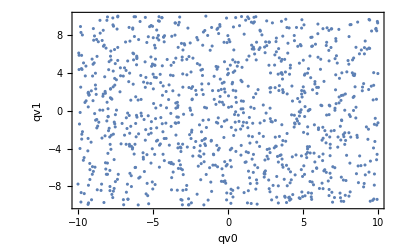

```mathematica
(*Some example plots*)
ListPlot[Transpose[{qv0List ,qv1List}], Frame->True, FrameLabel->{"qv0","qv1"}]
```

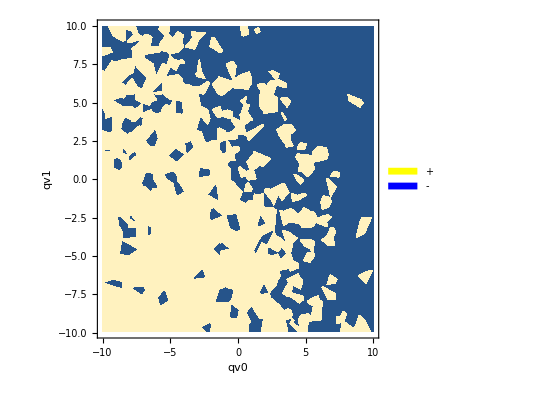

```mathematica
ListContourPlot[Transpose[{qv0List ,qv1List,signList}], InterpolationOrder->0,PlotLegends->SwatchLegend[{Yellow,Blue},{"+","-"},LegendMarkerSize->25],FrameLabel->{"qv0","qv1"}]
```

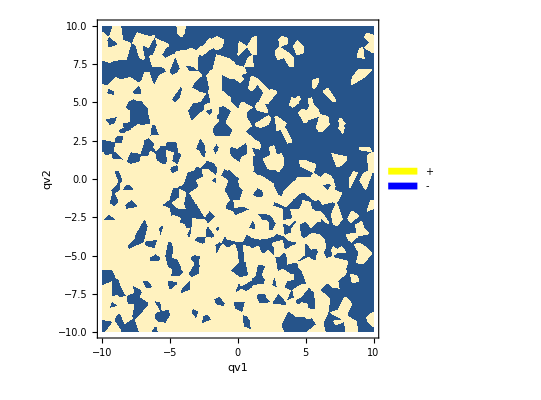

```mathematica
ListContourPlot[Transpose[{qv1List ,qv2List,signList}], InterpolationOrder->0,PlotLegends->SwatchLegend[{Yellow,Blue},{"+","-"},LegendMarkerSize->25],FrameLabel->{"qv1","qv2"}]
```

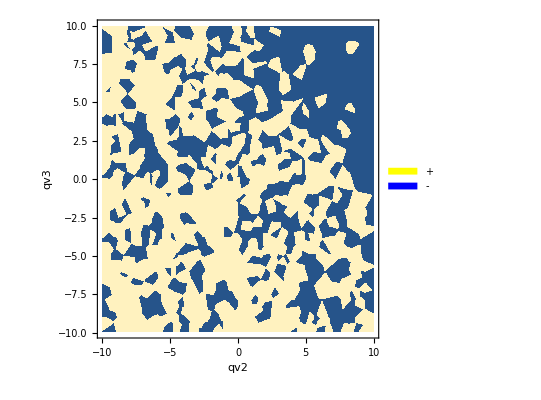

```mathematica
ListContourPlot[Transpose[{qv2List ,qv3List,signList}], InterpolationOrder->0,PlotLegends->SwatchLegend[{Yellow,Blue},{"+","-"},LegendMarkerSize->25],FrameLabel->{"qv2","qv3"}]
```

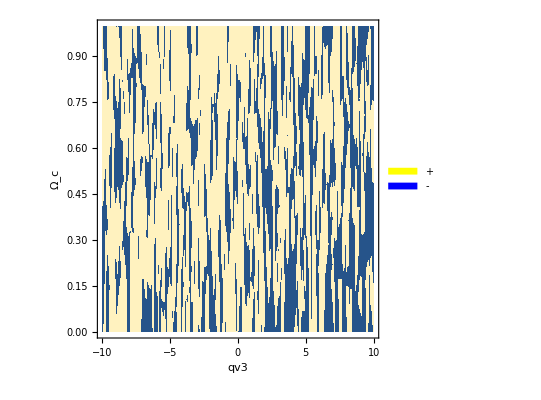

```mathematica
ListContourPlot[Transpose[{qv3List ,ΩcList,signList}], InterpolationOrder->0,PlotLegends->SwatchLegend[{Yellow,Blue},{"+","-"},LegendMarkerSize->25],FrameLabel->{"qv3","Ω_c"}]
```